```mathematica
(* Исходные параметры *)
m = 2;
F1[t_] = 3*t;
F2[t_] = 0;
F3[t_] = -2*t;

(* Кусочно заданная функция силы от времени*)
F[t_] = Piecewise[ 
{
{F1[t], t ≤ 5}, 
{F[5] + F2[t - 5], 5 < t ≤ 10},
{F[10] + F3[t - 10], t > 10}
}, 0
];

(* Функции ускорения и координаты от времени *)
a[t_] = F[t] / m;
x[t_] = Integrate[a[t], t];
```

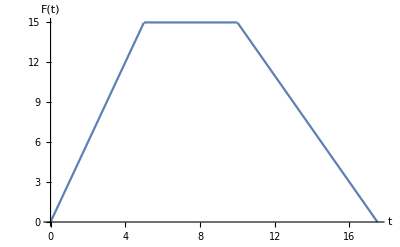

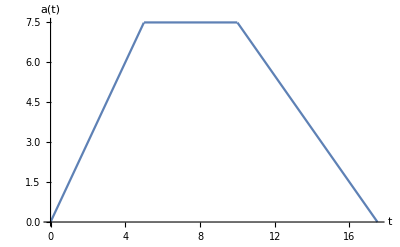

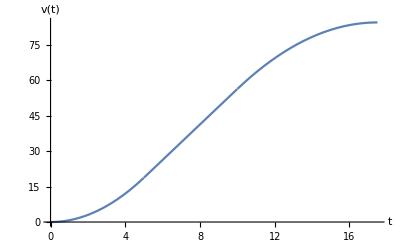

```mathematica
(* Построение графиков *)
Plot[F[t], {t, 0, 17.5}, AxesLabel->{t,"F(t)"}]
Plot[a[t], {t, 0, 17.5}, AxesLabel->{t,"a(t)"}]
Plot[x[t], {t, 0, 17.5}, AxesLabel->{t,"v(t)"}]
```